## Branch Lengths in Substitution Units

The probability that i lineages coalesce into j lineages in time T is shown by the function gij (T) (Tavaré  1984), and according to Rosenberg 2002, we have

```mathematica
g11[T_] := 1
g21[T_] := 1 - ⅇ^-T
g22[T_] := ⅇ^-T
g31[T_] := 1−3/2 ⅇ^(−T)+1/2 ⅇ^(−3T)
g32[T_] := 3/2 ⅇ^(−T)−3/2 ⅇ^(−3T)
g33[T_] := ⅇ^(−3T)
```

### Balanced Species Tree ((A, B):T1, (C, D):T2)

#### Internal branch

Matching

Conditional distribution of unrooted gene tree matching the species tree

```mathematica
FullSimplify[
g21[T1]g21[T2]+
1/3g21[T1]g22[T2]+
2/3g21[T1]g22[T2]+
1/3g22[T1]g21[T2]+
2/3g22[T1]g21[T2]+
1/9g22[T1]g22[T2]+
2/9g22[T1]g22[T2]]
```

1-(2 ⅇ^(-T1-T2))/3

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y]((T1-x)Subscript[μ, 1]+(T2-y) Subscript[μ, 2]+2 Subscript[μ, 3]),{x,0,T1},{y,0,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals]+
(ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*1/3*((T1-x)Subscript[μ, 1]+(y+2) Subscript[μ, 3]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
(ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*2/3*((T1-x)Subscript[μ, 1]+y Subscript[μ, 3]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*1/3*((T2-y)Subscript[μ, 2]+(x+2) Subscript[μ, 3]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*2/3*((T2-y)Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(2+y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]+
4(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]]
```

1/3 ⅇ^(-T1-T2) (3 ⅇ^T2 (μ_1-μ_3)+μ_3+3 ⅇ^T1 (μ_2-μ_3+ⅇ^T2 ((-1+T1) μ_1+(-1+T2) μ_2+2 μ_3)))

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elb[T1_,T2_,μ1_,μ2_,μ3_] := (1/3 ⅇ^(-T1-T2) (3 ⅇ^T2 (μ1-μ3)+μ3+3 ⅇ^T1 (μ2-μ3+ⅇ^T2 ((-1+T1) μ1+(-1+T2) μ2+2 μ3)))) /(1-2/3 ⅇ^(-T1-T2))
```

```mathematica
FullSimplify[elb[T1,T2,μ1,μ2,μ3]]
```

(3 ⅇ^T2 (μ1-μ3)+μ3+3 ⅇ^T1 (μ2-μ3+ⅇ^T2 ((-1+T1) μ1+(-1+T2) μ2+2 μ3)))/(-2+3 ⅇ^(T1+T2))

Simplifying the equations by setting

```mathematica
FullSimplify[elb[T1,T1,μ1,μ3-μ1,μ3]]
```

((1+3 ⅇ^T1 (-1+ⅇ^T1 (1+T1))) μ3)/(-2+3 ⅇ^(2 T1))

Simplifying the equations by letting  or

```mathematica
FullSimplify[Limit[elb[T1,T2,μ1,μ2,μ3], T1 -> 0]]
```

(3 (1+ⅇ^T2 (-1+T2)) μ2)/(-2+3 ⅇ^T2)+μ3

```mathematica
FullSimplify[Limit[elb[T1,T2,μ1,μ2,μ3], T2 -> 0]]
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)+μ3

Non-Matching

Conditional distribution of unrooted gene tree not matching the species tree

```mathematica
FullSimplify[
1/9g22[T1]g22[T2]+
2/9g22[T1]g22[T2]]
```

ⅇ^(-T1-T2)/3

Expected branch length

```mathematica
FullSimplify[
2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(2+y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]+
4(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]]
```

1/3 ⅇ^(-T1-T2) μ_3

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠ st))

```mathematica
eab[T1_,T2_,μ1_,μ2_,μ3_] :=( 1/3 ⅇ^(-T1-T2) μ3)/(ⅇ^(-T1-T2)/3)
```

```mathematica
FullSimplify[eab[T1,T2,μ1,μ2,μ3]]
```

μ3

Formula for internal branch length in SU

Computing the difference between el and ea

```mathematica
dif = FullSimplify[Limit[elb[T1,T2,μ1,μ2,μ3] - eab[T1,T2,μ1,μ2,μ3], T2 -> 0]]
d = T1
p = 1 - ⅇ^-d
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)

T1

1-ⅇ^-T1

The internal branch has the same formula as unbalanced (when T2=0)

```mathematica
FullSimplify[1 / 3 * dif * d * (1 + 2 * p) / (d - p)] ==d μ1
```

True

#### Pendant Branches

Pendant branch of A (and B)
Matching

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y](x Subscript[μ, 1]+ Subscript[T, A] Subscript[μ, A]),{x,0,T1},{y,0,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals]+
(ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*1/3*(x Subscript[μ, 1]+ Subscript[T, A] Subscript[μ, A]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
     (ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*2/3*(x Subscript[μ, 1]+ Subscript[T, A] Subscript[μ, A]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*1/3*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,0,T2},Assumptions->T1∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*1/3*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*1/3*((x+2) Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
     (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
  2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]]
```

1/9 ⅇ^(-T1-T2) ((9 ⅇ^T2 (-1+ⅇ^T1)-6 T1) μ_1+(-7+9 ⅇ^T2) μ_3+3 (-2+3 ⅇ^(T1+T2)) T_A μ_A)

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elbA[T1_,T2_,μ1_,μ2_,μ3_, μA_]:= (1/9 ⅇ^(-T1-T2) ((9 ⅇ^T2 (-1+ⅇ^T1)-6 T1) μ1+(-7+9 ⅇ^T2) μ3+3 (-2+3 ⅇ^(T1+T2)) Subscript[T, A] μA))/(1-(2 ⅇ^(-T1-T2))/3)
```

```mathematica
FullSimplify[elbA[T1,T2,μ1,μ2,μ3,μA ]]
```

(-6 T1 μ1-7 μ3+9 ⅇ^T2 ((-1+ⅇ^T1) μ1+μ3)+3 (-2+3 ⅇ^(T1+T2)) μA T_A)/(-6+9 ⅇ^(T1+T2))

Non-Matching (same for AD|BC and AC|BD)

```mathematica
FullSimplify[
  (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
    (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3]+ T1 Subscript[μ, 1] +Subscript[T, A] Subscript[μ, A]),{x,0,Infinity},{y,x,Infinity}]]
```

1/9 ⅇ^(-T1-T2) (3 T1 μ_1+2 μ_3+3 T_A μ_A)

```mathematica
eabA[T1_,T2_,μ1_,μ2_,μ3_, μA_]:= 1/9 ⅇ^(-T1-T2) (3 T1 μ1+2 μ3+3 Subscript[T, A] μA)/(ⅇ^(-T1-T2)/3)
```

```mathematica
FullSimplify[eabA[T1,T2,μ1,μ2,μ3,μA ]]
```

T1 μ1+(2 μ3)/3+μA T_A

Formula for pendant branch of A in SU

```mathematica
difbA = FullSimplify[elbA[T1,T2,μ1,μ2,μ1, μA]-eabA[T1,T2,μ1,μ2,μ1, μA]]
```

((-1+ⅇ^(T1+T2) (1-3 T1)) μ1)/(-2+3 ⅇ^(T1+T2))

Formula for T1

```mathematica
FullSimplify[1 / 3 * (p - difbA * (1 + 2 * p) / μ1)] ==T1
```

True

Pendant branch of C (and D)
Matching

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y](y Subscript[μ, 2]+ Subscript[T, C] Subscript[μ, C]),{x,0,T1},{y,0,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals]+
(ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*1/3*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
     (ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*1/3*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
(ⅇ^-T2)Integrate[Exp[-x]3Exp[-3y]*1/3*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,T1},{y,0,Infinity},Assumptions->T1∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*1/3*(y Subscript[μ, 2]+ Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
(ⅇ^-T1)Integrate[3Exp[-3x]Exp[-y]*2/3*(y Subscript[μ, 2]+ Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,0,T2},Assumptions->T2∈PositiveReals]+
     (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
  2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]]
```

μ_2+T_C μ_C+1/9 ⅇ^(-T1-T2) (-3 (3 ⅇ^T1+2 T2) μ_2+(-7+9 ⅇ^T1) μ_3-6 T_C μ_C)

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elbC[T1_,T2_,μ1_,μ2_,μ3_, μC_]:= (μ2+Subscript[T, C] μC+1/9 ⅇ^(-T1-T2) (-3 (3 ⅇ^T1+2 T2) μ2+(-7+9 ⅇ^T1) μ3-6 Subscript[T, C] μC))/(1-(2 ⅇ^(-T1-T2))/3)
```

```mathematica
FullSimplify[elbC[T1,T2,μ1,μ2,μ3,μC ]]
```

μ2+((6-9 ⅇ^T1-6 T2) μ2+(-7+9 ⅇ^T1) μ3)/(-6+9 ⅇ^(T1+T2))+μC T_C

```mathematica
(-6 (1+ⅇ^T1 (-1+T1)) μ1+(4-5 ⅇ^T1) μ2)/(-4+6 ⅇ^T1)
```

```mathematica
FullSimplify[Limit[elbC[T1,T2,μ1,μ2,μ3,μC ], T1->0]]
```

μ2+(3 μ2+6 T2 μ2-2 μ3)/(6-9 ⅇ^T2)+μC T_C

```mathematica
μ1+(3 μ1+6 T1 μ1-2 μ3)/(6-9 ⅇ^T1)+μa Subscript[T, a]
```

```mathematica
FullSimplify[elbA[T1,T2,μ1,μ2,μ3,μA ]- (μ1+((6-9 ⅇ^T2-6 T1) μ1+(-7+9 ⅇ^T2) μ3)/(-6+9 ⅇ^(T1+T2))+μA Subscript[T, A])]==0
```

True

```mathematica
FullSimplify[elbC[T1,T2,μ1,μ2,μ3,μC ]+elbA[T1,T2,μ1,μ2,μ3,μA ]]
```

-(9 ⅇ^T2 μ1+6 T1 μ1+6 T2 μ2+14 μ3-9 ⅇ^T2 μ3+6 μA T_A+6 μC T_C-9 ⅇ^T1 (-μ2+μ3+ⅇ^T2 (μ1+μ2+μA T_A+μC T_C)))/(-6+9 ⅇ^(T1+T2))

Non-Matching (same for AD|BC and AC|BD)

```mathematica
FullSimplify[
  (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
    (ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^-T1)(ⅇ^-T2)Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, C] Subscript[μ, C]+T2 Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}]]
```

1/9 ⅇ^(-T1-T2) (3 T2 μ_2+2 μ_3+3 T_C μ_C)

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st))

```mathematica
eabC[T1_,T2_,μ1_,μ2_,μ3_, μC_]:= (1/9 ⅇ^(-T1-T2) (3 T2 μ2+2 μ3+3 Subscript[T, C] μC))/(ⅇ^(-T1-T2)/3)
```

```mathematica
FullSimplify[eabC[T1,T2,μ1,μ2,μ3,μC ]]
```

T2 μ2+(2 μ3)/3+μC T_C

Formula for pendant branch of C in SU

```mathematica
FullSimplify[elbC[T1,T2,μ1,μ2,μ3, μC]-eabC[T1,T2,μ1,μ2,μ3, μC]]
```

(-μ3+ⅇ^T1 (-3 μ2+ⅇ^T2 (-3 (-1+T2) μ2-2 μ3)+3 μ3))/(-2+3 ⅇ^(T1+T2))

```mathematica
FullSimplify[elbC[T1,T2,μ1,μ3,μ3, μC]-eabC[T1,T2,μ1,μ3,μ3, μC]]
```

((-1+ⅇ^(T1+T2) (1-3 T2)) μ3)/(-2+3 ⅇ^(T1+T2))

```mathematica
FullSimplify[Limit[elbC[T1,T2,μ1,μ2,μ3, μC]-eabC[T1,T2,μ1,μ2,μ3, μC],T2->0]]
```

((-1+ⅇ^T1) μ3)/(-2+3 ⅇ^T1)

```mathematica
FullSimplify[Limit[elbC[T1,T2,μ1,μ2,μ3, μC]-eabC[T1,T2,μ1,μ2,μ3, μC],T1->0]]
```

(-3 (1+ⅇ^T2 (-1+T2)) μ2-2 (-1+ⅇ^T2) μ3)/(-2+3 ⅇ^T2)

```mathematica
difbC = FullSimplify[elbC[T1,T2,μ1,μ2,μ2, μC]-eabC[T1,T2,μ1,μ2,μ2, μC]]
d = T1 + T2
p = 1 - ⅇ^-d
```

((-1+ⅇ^(T1+T2) (1-3 T2)) μ2)/(-2+3 ⅇ^(T1+T2))

T1+T2

1-ⅇ^(-T1-T2)

Formula for T2

```mathematica
FullSimplify[1 / 3 * (p - difbC * (1 + 2 * p) / μ2)] ==T2
```

True

Formula for μCTC

```mathematica
FullSimplify[eabC[T1,T2,μ1,μ2,μ3,μC ] - (2 μ3)/3 -  1 / 3 * (μ2*p - difbC * (1 + 2 * p))] ==μC Subscript[T, C]
```

True

### Unbalanced Species Tree (((A, B):T1, C):T2, D)

#### Internal branch

Matching

Conditional distribution of unrooted gene tree matching the species tree (i.e. P(AB|CD))

```mathematica
FullSimplify[
g21[T1]g21[T2]+
1/3g21[T1]g22[T2]+
2/3g21[T1]g22[T2]+
1/3g22[T1]g31[T2]+
2/9g22[T1]g32[T2]+
1/9g22[T1]g32[T2]+
1/9g22[T1]g33[T2]+
2/9g22[T1]g33[T2]]
```

1-(2 ⅇ^-T1)/3

Expected Branch Lengths

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y]((Subscript[T, 1]-x)Subscript[μ, 1]+y Subscript[μ, 2]),{x,0,Subscript[T, 1]},{y,0,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*2/3*((Subscript[T, 1]-x)Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*((Subscript[T, 1]-x)Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))2/3((Subscript[T, 2]-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3((Subscript[T, 2]-x)Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(2+y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]+
4(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]]
```

1/6 ⅇ^(-T_1-3 T_2) (μ_2+ⅇ^(2 T_2) (6 ⅇ^T_2 (1+ⅇ^T_1 (-1+T_1)) μ_1+2 ⅇ^T_2 (-2+3 ⅇ^T_1) μ_2-3 (-1+2 ⅇ^T_1) (μ_2-μ_3))-μ_3)

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
el[T1_,T2_,μ1_,μ2_,μ3_]:=(1/6 ⅇ^(-T1-3 T2) (μ2+ⅇ^(2 T2) (6 ⅇ^T2 (1+ⅇ^T1 (-1+T1)) μ1+2 ⅇ^T2 (-2+3 ⅇ^T1) μ2-3 (-1+2 ⅇ^T1) (μ2-μ3))-μ3))/(1-(2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[el[T1,T2,μ1,μ2,μ3]]
```

(ⅇ^(-3 T2) (μ2-μ3+ⅇ^(2 T2) (6 ⅇ^T2 μ1+3 μ2-4 ⅇ^T2 μ2-3 μ3+6 ⅇ^T1 (-μ2+ⅇ^T2 ((-1+T1) μ1+μ2)+μ3))))/(2 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[el[T1,T2,μ1,μ2,μ3] - (((ⅇ^(-3 T2) +3 ⅇ^(- T2)-6 ⅇ^(T1 - T2)  )(μ2-μ3)+6 (1-ⅇ^T1 +T1 ⅇ^T1) μ1)/(2 (-2+3 ⅇ^T1)) + μ2)]
```

0

Simplifying the equations by setting

```mathematica
FullSimplify[el[T1,T2,μ1,μ2,μ2]]
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)+μ2

Check that setting  is equivalent to letting

```mathematica
FullSimplify[el[T1,T2,μ1,μ2,μ2]] == FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3],T2->Infinity]]
```

True

```mathematica
FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3],T2->0]]
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)+μ3

```mathematica
FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3],T2->Infinity]] - FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3],T2->0]]
```

μ2-μ3

Non-Matching

Conditional distribution of unrooted gene tree not matching the species tree

```mathematica
FullSimplify[
1/3g22[T1]g31[T2]+
2/9g22[T1]g32[T2]+
1/9g22[T1]g32[T2]+
1/9g22[T1]g33[T2]+
2/9g22[T1]g33[T2]]
```

ⅇ^-T1/3

Expected Branch Lengths

```mathematica
FullSimplify[
   (ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 (y-x)Subscript[μ, 2],{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))2/3((Subscript[T, 2]-x)Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3((Subscript[T, 2]-x)Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(2+y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]+
4(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y-x)Subscript[μ, 3],{x,0,Infinity},{y,x,Infinity}]]
```

1/6 ⅇ^(-T_1-3 T_2) ((-1+ⅇ^T_2)^2 (1+2 ⅇ^T_2) μ_2+(-1+3 ⅇ^(2 T_2)) μ_3)

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st))

```mathematica
ea[T1_,T2_,μ1_,μ2_,μ3_]:=(1/6 ⅇ^(-T1-3 T2) ((-1+ⅇ^T2)^2 (1+2 ⅇ^T2) μ2+(-1+3 ⅇ^(2 T2)) μ3))/(ⅇ^-T1/3)
```

```mathematica
FullSimplify[ea[T1,T2,μ1,μ2,μ3]]
```

μ2+1/2 ⅇ^(-3 T2) (μ2-μ3)-3/2 ⅇ^-T2 (μ2-μ3)

Simplifying the equations by setting

```mathematica
FullSimplify[ea[T1,T2,μ1,μ2,μ2]]
```

μ2

Check that setting  is equivalent to letting

```mathematica
FullSimplify[ea[T1,T2,μ1,μ2,μ2]] == FullSimplify[Limit[ea[T1,T2,μ1,μ2,μ3],T2->Infinity]]
```

True

```mathematica
FullSimplify[Limit[ea[T1,T2,μ1,μ2,μ3],T2->0]]
```

μ3

Formula for internal branch length in SU

Computing the difference between el and ea

```mathematica
FullSimplify[el[T1,T2,μ1,μ2,μ3] - ea[T1,T2,μ1,μ2,μ3]]
```

(3 ⅇ^(-3 T2) (μ2-μ3+ⅇ^(2 T2) (2 ⅇ^T2 μ1-μ2+μ3)+ⅇ^T1 (-μ2+ⅇ^(2 T2) (2 ⅇ^T2 (-1+T1) μ1+μ2-μ3)+μ3)))/(2 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[(el[T1,T2,μ1,μ2,μ3] - ea[T1,T2,μ1,μ2,μ3]) - ((3( ⅇ^(- T2)-ⅇ^(-3 T2) )(1 -ⅇ^-T1)(μ2-μ3) +6 μ1(ⅇ^-T1-1+T1))/(2 (3 -2 ⅇ^-T1)))]
```

0

Simplifying the equations by setting

```mathematica
dif = FullSimplify[el[T1,T2,μ1,μ2,μ2] - ea[T1,T2,μ1,μ2,μ2]]
d = T1;
p = 1 - ⅇ^-d;
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)

Formula for internal branch in SU

```mathematica
FullSimplify[1 / 3 * dif * d * (1 + 2 * p) / (d - p)] ==d μ1
```

True

```mathematica
Formula for internal branch in SU when d is very small
δ = diff/μ
m = CU estimate of the branch length
```

```mathematica
Series[Exp[T1],{T1,m ,2}]
```

ⅇ^m+ⅇ^m (T1-m)+1/2 ⅇ^m (T1-m)^2+O[T1-m]^3

```mathematica
FullSimplify[el[T1,T2,μ,μ,μ] ]
FullSimplify[ ea[T1,T2,μ,μ,μ]]
FullSimplify[Solve[(3 (1+(1+T1) (-1+T1)))/(-2+3 (1+T1))==δ,T1]]
FullSimplify[Solve[(3 (1+(ⅇ^m+ⅇ^m (T1-m)) (-1+T1)))/(-2+3 (ⅇ^m+ⅇ^m (T1-m)))==δ,T1]]
FullSimplify[SolveValues[(3 (1+(1+T1+1/2T1^2) (-1+T1)))/(-2+3 (1+T1+1/2T1^2 ))==δ ,T1][[1]]]
```

((1+3 ⅇ^T1 T1) μ)/(-2+3 ⅇ^T1)

μ

{{T1→1/6 (3 δ-√3 √(δ (4+3 δ)))},{T1→1/6 (3 δ+√3 √(δ (4+3 δ)))}}

{{T1→1/6 (3 (m+δ)+√3 ⅇ^-m √(ⅇ^m (3 ⅇ^m (2-m+δ)^2-4 (3+2 δ))))},{T1→1/6 (3 (m+δ)-√3 ⅇ^-m √(ⅇ^m (3 ⅇ^m (2-m+δ)^2-4 (3+2 δ))))}}

1/3 (-1+δ+(1+δ (4+δ))/(-1+δ (3+δ (6+δ))+3 √(-δ (2+δ (6+δ (6+δ)))))^(1/3)+(-1+δ (3+δ (6+δ))+3 √(-δ (2+δ (6+δ (6+δ)))))^(1/3))

```mathematica
FullSimplify[Solve[(3 (1+(ⅇ^m+ⅇ^m (T1-m)+1/2 ⅇ^m (T1-m)^2) (-1+T1)))/(-2+3 (ⅇ^m+ⅇ^m (T1-m)+1/2 ⅇ^m (T1-m)^2))==δ ,T1]]
```

{{T1→1/3 (-1+2 m+δ+(ⅇ^m (1+m^2-2 m (2+δ)+δ (4+δ)))/((ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))+ⅇ^-m (ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))},{T1→1/6 (2 (-1+2 m+δ)-(ⅈ (-ⅈ+√3) ⅇ^m (1+m^2-2 m (2+δ)+δ (4+δ)))/((ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))+ⅈ (ⅈ+√3) ⅇ^-m (ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))},{T1→1/6 (2 (-1+2 m+δ)+(ⅈ (ⅈ+√3) ⅇ^m (1+m^2-2 m (2+δ)+δ (4+δ)))/((ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))-ⅈ (-ⅈ+√3) ⅇ^-m (ⅇ^(2 m) (-9 (3+2 δ)+ⅇ^m (2-m+δ) (13+m^2-2 m (2+δ)+δ (4+δ)))+3 √(ⅇ^(4 m) (9 (3+2 δ)^2+3 ⅇ^(2 m) (5+m^2-2 m (2+δ)+δ (4+δ))^2+2 ⅇ^m (-2+m-δ) (3+2 δ) (13+m^2-2 m (2+δ)+δ (4+δ)))))^(1/3))}}

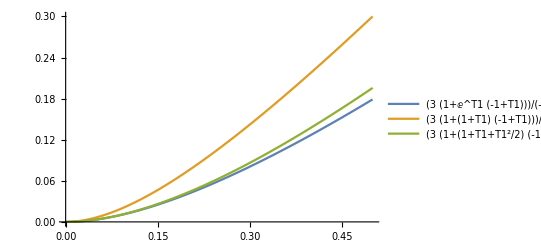

```mathematica
Plot[{(3 (1+ⅇ^T1 (-1+T1)))/(-2+3 ⅇ^T1),(3 (1+(1+T1) (-1+T1)))/(-2+3 (1+T1)),(3 (1+(1+T1+1/2T1^2) (-1+T1)))/(-2+3 (1+T1+1/2T1^2 ))},{T1,0,.5},PlotLegends->"Expressions"]
```

```mathematica
Solve[(3 (1+ⅇ^T1 (-1+T1)))/(-2+3 ⅇ^T1)==δ, T1]
Series[ProductLog[x],{x,-ⅇ^-1 ,5}]
ts[x_]:=-1+√(2 ⅇ) √(x+1/ⅇ)-2/3 ⅇ (x+1/ⅇ)+(11 ⅇ^(3/2) (x+1/ⅇ)^(3/2))/(18 √2)-43/135 ⅇ^2 (x+1/ⅇ)^2+(769 ⅇ^(5/2) (x+1/ⅇ)^(5/2))/(2160 √2)-(1768 ⅇ^3 (x+1/ⅇ)^3)/8505
FullSimplify[1+δ+ts[-1/3 ⅇ^(-1-δ) (3+2 δ)]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T1→1+δ+ProductLog[-1/3 ⅇ^(-1-δ) (3+2 δ)]}}

-1+√(2 ⅇ) √(x+1/ⅇ)-2/3 ⅇ (x+1/ⅇ)+(11 ⅇ^(3/2) (x+1/ⅇ)^(3/2))/(18 √2)-43/135 ⅇ^2 (x+1/ⅇ)^2+(769 ⅇ^(5/2) (x+1/ⅇ)^(5/2))/(2160 √2)-(1768 ⅇ^3 (x+1/ⅇ)^3)/8505+O[x+1/ⅇ]^(11/2)

-2/3+δ+2/9 ⅇ^-δ (3+2 δ)+(11 (3-ⅇ^-δ (3+2 δ))^(3/2))/(54 √6)+(769 (3-ⅇ^-δ (3+2 δ))^(5/2))/(19440 √6)-(1768 (3-ⅇ^-δ (3+2 δ))^3)/229635+√(2-2/3 ⅇ^-δ (3+2 δ))-(43 (-3+ⅇ^-δ (3+2 δ))^2)/1215

0.

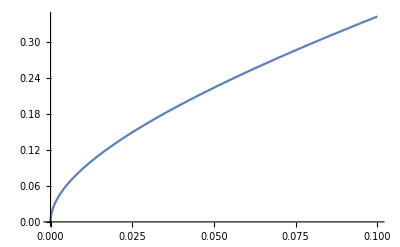

```mathematica
est[δ_]:=-2/3+δ+2/9 ⅇ^-δ (3+2 δ)+(11 (3-ⅇ^-δ (3+2 δ))^(3/2))/(54 √6)+(769 (3-ⅇ^-δ (3+2 δ))^(5/2))/(19440 √6)-(1768 (3-ⅇ^-δ (3+2 δ))^3)/229635+√(2-2/3 ⅇ^-δ (3+2 δ))-(43 (-3+ⅇ^-δ (3+2 δ))^2)/1215
Round[est[0],0.000001]
Plot[est[δ],{δ,0,.1}]
```

```mathematica
Series[ProductLog[x],{x,0,5}]
```

x-x^2+(3 x^3)/2-(8 x^4)/3+(125 x^5)/24+O[x]^6

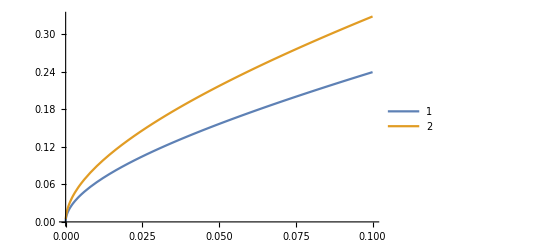

```mathematica
Plot[{1/6 (3 δ+√3 √(δ (4+3 δ))),1/3 (-1+δ+(1+δ (4+δ))/(-1+δ (3+δ (6+δ))+3 √(-δ (2+δ (6+δ (6+δ)))))^(1/3)+(-1+δ (3+δ (6+δ))+3 √(-δ (2+δ (6+δ (6+δ)))))^(1/3))},{δ,0,0.1},PlotLegends->Automatic]
```

```mathematica
FullSimplify[Solve[(1+3 (T1+1) T1)/(-2+3 (T1+1))==x,T1]]
FullSimplify[Solve[(1+3 (T1+1+1/2T1^2) T1)/(-2+3 (T1+1+1/2T1^2))==x,T1][[1]]]
```

Formula for μ1

```mathematica
FullSimplify[1 / 3 * dif * (1 + 2 * p) / (d - p)] ==μ1
```

True

Analyzing the behavior of the formula

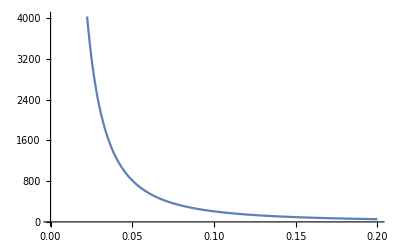

```mathematica
Plot[1/(d-1+Exp[-d]),{d,0.000001,0.2}]
```

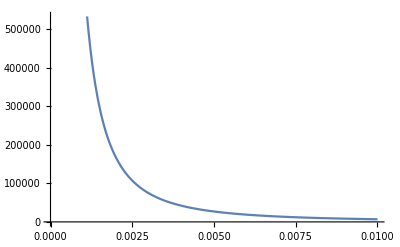

```mathematica
Plot[1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]),{d,0.000001,0.01}]
```

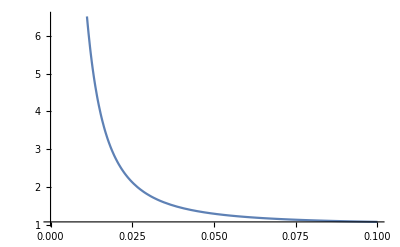

```mathematica
Plot[1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]) * (1/((1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]))) + 0.001),{d,0.000001,0.1}]
```

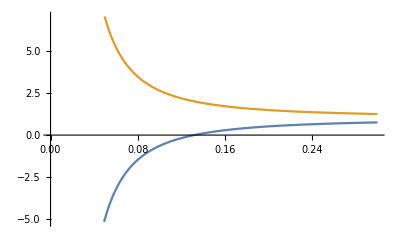

```mathematica
Plot[{1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]) * (1/((1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]))) - 0.02),1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]) * (1/((1/3  * (1 + 2 * (1 - Exp[-d])) /(d-1+Exp[-d]))) + 0.02)},{d,0.000001,0.3}]
```

```mathematica
FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3]-ea[T1,T2,μ1,μ2,μ3],T2->0]]
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)

```mathematica
FullSimplify[Limit[el[T1,T2,μ1,μ2,μ3]-ea[T1,T2,μ1,μ2,μ3],T2->Infinity]]
```

(3 (1+ⅇ^T1 (-1+T1)) μ1)/(-2+3 ⅇ^T1)

#### Pendant Branches

Pendant branch of A
Matching

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x](x Subscript[μ, 1]+ Subscript[T, a] Subscript[μ, a]),{x,0,Subscript[T, 1]},Assumptions->Subscript[T, 1]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 ( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/9 ⅇ^(-T_1-3 T_2) (-μ_2+2 μ_3+ⅇ^(3 T_2) ((-9+9 ⅇ^T_1-6 T_1) μ_1+μ_2+3 (-2+3 ⅇ^T_1) T_a μ_a))

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elA[T1_,T2_,μ1_,μ2_,μ3_, μa_]:= (1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) ((-9+9 ⅇ^T1-6 T1) μ1+μ2+3 (-2+3 ⅇ^T1) Subscript[T, a] μa)))/(1-(2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ3,μa ]]
```

((9-9 ⅇ^T1+6 T1) μ1-μ2+ⅇ^(-3 T2) (μ2-2 μ3)-3 (-2+3 ⅇ^T1) μa T_a)/(6-9 ⅇ^T1)

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ3,μa ] - ((6 T1 μ1 + 3μ1-μ2+ⅇ^(-3 T2) (μ2-2 μ3))/(6-9 ⅇ^T1) +μ1+ μa Subscript[T, a])]
```

0

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ2,μa ]]
```

((9-9 ⅇ^T1+6 T1) μ1+(-1-ⅇ^(-3 T2)) μ2-3 (-2+3 ⅇ^T1) μa T_a)/(6-9 ⅇ^T1)

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
```

μ1+(-3 (1+2 T1) μ1+μ2)/(-6+9 ⅇ^T1)+μa T_a

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

μ1+(3 μ1+6 T1 μ1-2 μ3)/(6-9 ⅇ^T1)+μa T_a

Setting  is not equivalent to letting

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ2,μa ] - Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]] ==0
```

-(ⅇ^(-3 T2) μ2)/(6-9 ⅇ^T1)==0

```mathematica
FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

μ1+(3 μ1+6 T1 μ1-2 μ3)/(6-9 ⅇ^T1)+μa T_a

```mathematica
FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity] - Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

(μ2-2 μ3)/(-6+9 ⅇ^T1)

```mathematica
Plot3D[((9+6 d-9 ⅇ^d) +(-1-ⅇ^(-3 c)))/(6-9 ⅇ^d) - (d +2/3 (2-ⅇ^(-3 c)) ),{c,0,1},{d,0,2}]
```

-Graphics3D-

Non-Matching (AD|BC)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+y Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/18 ⅇ^(-T_1-3 T_2) (μ_2-5 μ_3+ⅇ^(2 T_2) (-9 μ_2+9 μ_3+2 ⅇ^T_2 (3 T_1 μ_1+4 μ_2+3 T_a μ_a)))

Non-Matching (AC|BD)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]2/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, a] Subscript[μ, a]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/9 ⅇ^(-T_1-3 T_2) (-μ_2+2 μ_3+ⅇ^(3 T_2) (3 T_1 μ_1+μ_2+3 T_a μ_a))

```mathematica
eaA2[T1_,T2_,μ1_,μ2_,μ3_, μa_]:= (1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) (3 T1 μ1+μ2+3 Subscript[T, a] μa)))/(ⅇ^-T1/3)
```

```mathematica
FullSimplify[eaA2[T1,T2,μ1,μ2,μ3, μa]]
```

1/3 (3 T1 μ1+μ2-ⅇ^(-3 T2) (μ2-2 μ3)+3 μa T_a)

```mathematica
FullSimplify[eaA2[T1,T2,μ1,μ2,μ3, μa] - (-1/3 ⅇ^(-3 T2) (μ2-2 μ3)+1/3 μ2+T1 μ1+ μa Subscript[T, a])]
```

0

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st)), with only AD|BC distribution

```mathematica
eaA[T1_,T2_,μ1_,μ2_,μ3_, μa_]:= 1/18 ⅇ^(-T1-3 T2) (μ2-5 μ3+ⅇ^(2 T2) (-9 μ2+9 μ3+2 ⅇ^T2 (3 T1 μ1+4 μ2+3 Subscript[T, a] μa))) / (ⅇ^-T1/3)
```

Considering the two different distributions

```mathematica
eaACorrect[T1_,T2_,μ1_,μ2_,μ3_, μa_]:= (1/18 ⅇ^(-T1-3 T2) (μ2-5 μ3+ⅇ^(2 T2) (-9 μ2+9 μ3+2 ⅇ^T2 (3 T1 μ1+4 μ2+3 Subscript[T, a] μa))) + 1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) (3 T1 μ1+μ2+3 Subscript[T, a] μa))) / ((2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[eaA[T1,T2,μ1,μ2,μ3, μa]]
```

1/6 ⅇ^(-3 T2) (μ2-5 μ3+ⅇ^(2 T2) (-9 μ2+9 μ3+2 ⅇ^T2 (3 T1 μ1+4 μ2+3 μa T_a)))

```mathematica
FullSimplify[eaA[T1,T2,μ1,μ2,μ3, μa] - ((1/6 ⅇ^(-3 T2)-3/2 ⅇ^-T2) (μ2- μ3)-2/3 ⅇ^(-3 T2) μ3 +4/3 μ2+T1 μ1+ μa Subscript[T, a])]
```

0

```mathematica
FullSimplify[eaACorrect[T1,T2,μ1,μ2,μ3, μa]]
```

T1 μ1+1/12 (10 μ2-9 ⅇ^-T2 (μ2-μ3)-ⅇ^(-3 T2) (μ2+μ3))+μa T_a

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[eaA[T1,T2,μ1,μ2,μ2, μa]]
```

T1 μ1+2/3 (2-ⅇ^(-3 T2)) μ2+μa T_a

```mathematica
FullSimplify[eaACorrect[T1,T2,μ1,μ2,μ2, μa]]
```

T1 μ1+1/6 (5-ⅇ^(-3 T2)) μ2+μa T_a

the two distributions have different formulas for pendant branches of A and B

```mathematica
FullSimplify[1/3 (3 T1 μ1+μ2+ⅇ^(-3 T2) μ2+3 μA Subscript[T, A]) - (T1 μ1+2/3 (2-ⅇ^(-3 T2)) μ2+μA TA)]
```

(-1+ⅇ^(-3 T2)) μ2

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
```

T1 μ1+(4 μ2)/3+μa T_a

```mathematica
FullSimplify[Limit[eaACorrect[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
```

T1 μ1+(5 μ2)/6+μa T_a

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

T1 μ1+(2 μ3)/3+μa T_a

```mathematica
FullSimplify[Limit[eaACorrect[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

T1 μ1+(2 μ3)/3+μa T_a

Setting  is not equivalent to letting

```mathematica
FullSimplify[eaA[T1,T2,μ1,μ2,μ2, μa] - Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
```

-2/3 ⅇ^(-3 T2) μ2

```mathematica
FullSimplify[Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity] - Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

2/3 (2 μ2-μ3)

Formula for pendant branch of A in SU

Computing the difference between elA and eaA

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ3, μa] - eaA[T1,T2,μ1,μ2,μ3, μa]]
```

(ⅇ^(-3 T2) (-6 ⅇ^(2 T2) (ⅇ^T2 (μ1-μ2)+μ2-μ3)-2 μ3+ⅇ^T1 (ⅇ^(3 T2) (-6 (-1+T1) μ1-8 μ2)-μ2+9 ⅇ^(2 T2) (μ2-μ3)+5 μ3)))/(2 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ3, μa] - eaACorrect[T1,T2,μ1,μ2,μ3, μa]]
```

(ⅇ^(-3 T2) (2 (-μ2+ⅇ^(3 T2) (-6 μ1+4 μ2)-3 ⅇ^(2 T2) (μ2-μ3)+μ3)+ⅇ^T1 (μ2-2 ⅇ^(3 T2) (6 (-1+T1) μ1+5 μ2)+9 ⅇ^(2 T2) (μ2-μ3)+μ3)))/(4 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[(elA[T1,T2,μ1,μ2,μ3, μa] - eaACorrect[T1,T2,μ1,μ2,μ3, μa]) - (1/(2 (-2+3 ⅇ^T1)) (4 μ2-6 μ1-(3  ⅇ^(- T2)+ⅇ^(-3 T2))(μ2-μ3)+ ⅇ^T1(1/2 (μ2+μ3)ⅇ^(-3 T2)+9/2  ⅇ^-T2(μ2-μ3)-6 T1 μ1-5 μ2 + 6 μ1)))]
```

0

Simplifying the equations by letting

```mathematica
difA =FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity] - Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
d = T1
p = 1 - ⅇ^-d
```

(-3 (1+ⅇ^T1 (-1+T1)) μ1+(3-4 ⅇ^T1) μ2)/(-2+3 ⅇ^T1)

T1

1-ⅇ^-T1

```mathematica
dif2A =FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa]-eaA[T1,T2,μ1,μ2,μ3, μa],T2->0]]
```

(-3 (1+ⅇ^T1 (-1+T1)) μ1-2 (-1+ⅇ^T1) μ3)/(-2+3 ⅇ^T1)

```mathematica
dif3A =FullSimplify[Limit[elA[T1,T2,μ1,μ2,μ3, μa]-eaACorrect[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
```

(-6 (1+ⅇ^T1 (-1+T1)) μ1+(4-5 ⅇ^T1) μ2)/(-4+6 ⅇ^T1)

```mathematica
FullSimplify[elA[T1,T2,μ1,μ2,μ2, μa]-eaACorrect[T1,T2,μ1,μ2,μ2, μa]]
```

(6 (1+ⅇ^T1 (-1+T1)) μ1+(-4+ⅇ^T1 (5-ⅇ^(-3 T2))) μ2)/(4-6 ⅇ^T1)

Formula for μ2

```mathematica
FullSimplify[-(μ1 * 3 * (d-p) +difA * (1 + 2 * p)) / (1+3*p)] == μ2
```

True

```mathematica
FullSimplify[-2(μ1 * 3 * (d-p) +dif3A * (1 + 2 * p)) / (1+4*p)] == μ2
```

True

Formula for μ3

```mathematica
FullSimplify[-(μ1 * 3 * (d-p) +dif2A * (1 + 2 * p)) / (2*p)] == μ3
```

True

Formula for μaTa (assuming )

```mathematica
eaAlim = FullSimplify[Limit[eaA[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
FullSimplify[eaAlim - T1 μ1-(4 μ2)/3] ==μa Subscript[T, a]
```

T1 μ1+(4 μ2)/3+μa T_a

True

```mathematica
eaACorrectlim = FullSimplify[Limit[eaACorrect[T1,T2,μ1,μ2,μ3, μa],T2->Infinity]]
FullSimplify[eaACorrectlim - T1 μ1-(5 μ2)/6] ==μa Subscript[T, a]
```

T1 μ1+(5 μ2)/6+μa T_a

True

Formula for μaTa (assuming )

```mathematica
eaAlim = FullSimplify[Limit[eaACorrect[T1,T2,μ1,μ2,μ3, μa],T2->0]]
FullSimplify[eaAlim - T1 μ1-(2 μ3)/3] ==μa Subscript[T, a]
```

T1 μ1+(2 μ3)/3+μa T_a

True

Pendant branch of B
Matching (same as A)

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x](x Subscript[μ, 1]+ Subscript[T, B] Subscript[μ, B]),{x,0,Subscript[T, 1]},Assumptions->Subscript[T, 1]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 ( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/9 ⅇ^(-T_1-3 T_2) (-μ_2+2 μ_3+ⅇ^(3 T_2) ((-9+9 ⅇ^T_1-6 T_1) μ_1+μ_2+3 (-2+3 ⅇ^T_1) T_B μ_B))

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elB[T1_,T2_,μ1_,μ2_,μ3_, μB_]:= (1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) ((-9+9 ⅇ^T1-6 T1) μ1+μ2+3 (-2+3 ⅇ^T1) Subscript[T, B] μB)))/(1-(2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[elB[T1,T2,μ1,μ2,μ3,μB ]]
```

((9-9 ⅇ^T1+6 T1) μ1-μ2+ⅇ^(-3 T2) (μ2-2 μ3)-3 (-2+3 ⅇ^T1) μB T_B)/(6-9 ⅇ^T1)

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[elB[T1,T2,μ1,μ2,μ2,μB ]]
```

((9-9 ⅇ^T1+6 T1) μ1+(-1-ⅇ^(-3 T2)) μ2-3 (-2+3 ⅇ^T1) μB T_B)/(6-9 ⅇ^T1)

Non-Matching (AD|BC)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]2/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+x Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/9 ⅇ^(-T_1-3 T_2) (-μ_2+2 μ_3+ⅇ^(3 T_2) (3 T_1 μ_1+μ_2+3 T_B μ_B))

Non-Matching (AC|BD)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+y Subscript[μ, 2]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y]Exp[-(Subscript[T, 2]-x)]1/3( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+x Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+y Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*( Subscript[T, B] Subscript[μ, B]+Subscript[T, 1] Subscript[μ, 1]+Subscript[T, 2] Subscript[μ, 2]+(y+2) Subscript[μ, 3]),{x,0,Infinity},{y,x,Infinity}, Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]]
```

1/18 ⅇ^(-T_1-3 T_2) (μ_2-5 μ_3+ⅇ^(2 T_2) (-9 μ_2+9 μ_3+2 ⅇ^T_2 (3 T_1 μ_1+4 μ_2+3 T_B μ_B)))

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st))

```mathematica
eaB[T1_,T2_,μ1_,μ2_,μ3_, μB_]:= 1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) (3 T1 μ1+μ2+3 Subscript[T, B] μB)) / (ⅇ^-T1/3)
```

```mathematica
FullSimplify[eaB[T1,T2,μ1,μ2,μ3, μB]]
```

1/3 (3 T1 μ1+μ2-ⅇ^(-3 T2) (μ2-2 μ3)+3 μB T_B)

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[eaB[T1,T2,μ1,μ2,μ2, μB]]
```

1/3 (3 T1 μ1+μ2+ⅇ^(-3 T2) μ2+3 μB T_B)

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaB[T1,T2,μ1,μ2,μ3, μB],T2->Infinity]]
```

T1 μ1+μ2/3+μB T_B

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaB[T1,T2,μ1,μ2,μ3, μB],T2->0]]
```

T1 μ1+(2 μ3)/3+μB T_B

Formula for pendant branch of B in SU

Computing the difference between elB and eaB

```mathematica
FullSimplify[elB[T1,T2,μ1,μ2,μ3, μB] - eaB[T1,T2,μ1,μ2,μ3, μB]]
```

(ⅇ^(-3 T2) (-μ2+ⅇ^(3 T2) (-3 μ1+μ2)+ⅇ^T1 (μ2-ⅇ^(3 T2) (3 (-1+T1) μ1+μ2)-2 μ3)+2 μ3))/(-2+3 ⅇ^T1)

Simplifying the equations by letting

```mathematica
difB =FullSimplify[Limit[elB[T1,T2,μ1,μ2,μ3, μB],T2->Infinity] - Limit[eaB[T1,T2,μ1,μ2,μ3, μB],T2->Infinity]]
d = T1
p = 1 - ⅇ^-d
```

(-3 μ1+μ2-ⅇ^T1 (3 (-1+T1) μ1+μ2))/(-2+3 ⅇ^T1)

T1

1-ⅇ^-T1

```mathematica
difB =FullSimplify[elB[T1,T2,μ1,μ2,μ2, μB]-eaB[T1,T2,μ1,μ2,μ2, μB]]
```

(ⅇ^(-3 T2) (μ2-ⅇ^T1 μ2+ⅇ^(3 T2) (-3 μ1+μ2)-ⅇ^(T1+3 T2) (3 (-1+T1) μ1+μ2)))/(-2+3 ⅇ^T1)

Pendant branch of C
Matching

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y](y Subscript[μ, 2]+ Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 1]},{y,0,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*((y+2) Subscript[μ, 3] +Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*(y Subscript[μ, 3] +Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 *(y Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3*((y+2) Subscript[μ, 3] +Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]]
```

1/18 ⅇ^(-T_1-3 T_2) ((-1+ⅇ^T_2) (-1+ⅇ^T_2 (-1+2 ⅇ^T_2 (-5+9 ⅇ^T_1))) μ_2+(-5+9 ⅇ^(2 T_2) (-1+2 ⅇ^T_1)) μ_3+6 ⅇ^(3 T_2) (-2+3 ⅇ^T_1) T_C μ_C)

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elC[T1_,T2_,μ1_,μ2_,μ3_, μC_]:= (1/18 ⅇ^(-T1-3 T2) ((-1+ⅇ^T2) (-1+ⅇ^T2 (-1+2 ⅇ^T2 (-5+9 ⅇ^T1))) μ2+(-5+9 ⅇ^(2 T2) (-1+2 ⅇ^T1)) μ3+6 ⅇ^(3 T2) (-2+3 ⅇ^T1) Subscript[T, C] μC))/(1-(2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[elC[T1,T2,μ1,μ2,μ3,μC ]]
```

μ2+(ⅇ^(-3 T2) (μ2+2 ⅇ^(3 T2) μ2-3 ⅇ^(2 T2) (μ2-μ3)-5 μ3))/(6 (-2+3 ⅇ^T1))+ⅇ^-T2 (-μ2+μ3)+μC T_C

```mathematica
FullSimplify[elC[T1,T2,μ1,μ2,μ3,μC ] - (-ⅇ^-T2 (μ2 - μ3)+(-4μ3 ⅇ^(-3 T2) + 2μ2-(3 ⅇ^-T2 -ⅇ^(-3 T2)) (μ2-μ3))/(6 (-2+3 ⅇ^T1))+μ2+μC Subscript[T, C])]
```

0

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[elC[T1,T2,μ1,μ2,μ2,μC ]]
```

((5-9 ⅇ^T1+2 ⅇ^(-3 T2)) μ2)/(6-9 ⅇ^T1)+μC T_C

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elC[T1,T2,μ1,μ2,μ3, μC],T2->Infinity]]
```

μ2+μ2/(-6+9 ⅇ^T1)+μC T_C

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elC[T1,T2,μ1,μ2,μ3, μC],T2->0]]
```

μ3+μ3/(6-9 ⅇ^T1)+μC T_C

Non-Matching (AD|BC)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 (x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))2/3(x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]]
```

1/9 ⅇ^(-T_1-3 T_2) (-μ_2+2 μ_3+ⅇ^(3 T_2) (μ_2+3 T_C μ_C))

Non-Matching (AC|BD)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 (x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))2/3(x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(x Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, 2] Subscript[μ, 2] + Subscript[T, C] Subscript[μ, C]),{x,0,Infinity},{y,x,Infinity}]]
```

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st))

```mathematica
eaC[T1_,T2_,μ1_,μ2_,μ3_, μC_]:= (1/9 ⅇ^(-T1-3 T2) (-μ2+2 μ3+ⅇ^(3 T2) (μ2+3 Subscript[T, C] μC)))/(ⅇ^-T1/3)
```

```mathematica
FullSimplify[eaC[T1,T2,μ1,μ2,μ3, μC]]
```

1/3 (μ2-ⅇ^(-3 T2) (μ2-2 μ3)+3 μC T_C)

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[eaC[T1,T2,μ1,μ2,μ2, μC]]
```

1/3 (μ2+ⅇ^(-3 T2) μ2+3 μC T_C)

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaC[T1,T2,μ1,μ2,μ3, μC],T2->Infinity]]
```

μ2/3+μC T_C

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[eaC[T1,T2,μ1,μ2,μ3, μC],T2->0]]
```

(2 μ3)/3+μC T_C

Formula for pendant branch of C in SU

Computing the difference between elC and eaC

```mathematica
FullSimplify[elC[T1,T2,μ1,μ2,μ3, μC] - eaC[T1,T2,μ1,μ2,μ3, μC]]
```

(ⅇ^(-3 T2) ((-1+2 ⅇ^T1) (-1+ⅇ^T2)^2 (1+2 ⅇ^T2) μ2+μ3-4 ⅇ^T1 μ3+3 ⅇ^(2 T2) (-1+2 ⅇ^T1) μ3))/(2 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[(elC[T1,T2,μ1,μ2,μ3, μC] - eaC[T1,T2,μ1,μ2,μ3, μC]) - (((2- ⅇ^-T1) ((ⅇ^(-3 T2) + 2 )μ2- 3 ⅇ^-T2(μ2- μ3))+μ3 ⅇ^(-3 T2)(ⅇ^-T1-4 ))/(2 (3 -2 ⅇ^-T1)))]
```

0

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elC[T1,T2,μ1,μ2,μ3, μC] - eaC[T1,T2,μ1,μ2,μ3, μC],T2->Infinity]]
```

(μ2-2 ⅇ^T1 μ2)/(2-3 ⅇ^T1)

```mathematica
FullSimplify[Limit[elC[T1,T2,μ1,μ2,μ3, μC] - eaC[T1,T2,μ1,μ2,μ3, μC],T2->0]]
```

((-1+ⅇ^T1) μ3)/(-2+3 ⅇ^T1)

Simplifying the equations by setting

```mathematica
FullSimplify[elC[T1,T2,μ1,μ2,μ2, μC] - eaC[T1,T2,μ1,μ2,μ2, μC]]
```

((1+ⅇ^T1 (-2+ⅇ^(-3 T2))) μ2)/(2-3 ⅇ^T1)

```mathematica
difC = FullSimplify[elC[T1,T2,μ1,μ2,μ2, μC] - eaC[T1,T2,μ1,μ2,μ2, μC]]
d = T1
p = 1 - Exp[-d]
```

((1+ⅇ^T1 (-2+ⅇ^(-3 T2))) μ2)/(2-3 ⅇ^T1)

T1

1-ⅇ^-T1

Formula for T2

```mathematica
FullSimplify[-Log[p + 1 - (difC * (1 + 2 * p) / μ2)]/3] == T2
```

-1/3 Log[ⅇ^(-3 T2)]==T2

(Alternate) Formula for μ2

```mathematica
dif2C = FullSimplify[Limit[elC[T1,T2,μ1,μ2,μ3, μC] - eaC[T1,T2,μ1,μ2,μ3, μC],T2->Infinity]]
FullSimplify[dif2C * (1 + 2 * p) / (1 + p)] == μ2
```

(μ2-2 ⅇ^T1 μ2)/(2-3 ⅇ^T1)

True

Formula for μCTC

```mathematica
eaClim = FullSimplify[Limit[eaC[T1,T2,μ1,μ2,μ3, μC],T2->Infinity]]
FullSimplify[eaClim - (dif2C * (2 - 1/(p+1)))/3] ==μC Subscript[T, C]
```

μ2/3+μC T_C

True

Pendant branch of D
Matching

Expected Branch Length

```mathematica
FullSimplify[
Integrate[Exp[-x]Exp[-y]((Subscript[T, 2]-y)Subscript[μ, 2]+2 Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 1]},{y,0,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*((y+2) Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 2]))Integrate[Exp[-x]Exp[-3y]3*1/3*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 1]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 ((Subscript[T, 2]-y)Subscript[μ, 2]+2 Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3((y+2) Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 1]∈PositiveReals&&Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]]
```

1/18 ⅇ^(-T_1-3 T_2) ((-1+ⅇ^(2 T_2) (-9+18 ⅇ^T_1-2 ⅇ^T_2 (-5+9 ⅇ^T_1))+6 ⅇ^(3 T_2) (-2+3 ⅇ^T_1) T_2) μ_2+μ_3+3 ⅇ^(2 T_2) (-3 (-1+2 ⅇ^T_1) μ_3+2 ⅇ^T_2 (-2+3 ⅇ^T_1) (2 μ_3+T_D μ_D)))

Expected branch length conditioned on gene tree matching the species tree (E(L|gt = st))

```mathematica
elD[T1_,T2_,μ1_,μ2_,μ3_, μD_]:= (1/18 ⅇ^(-T1-3 T2) ((-1+ⅇ^(2 T2) (-9+18 ⅇ^T1-2 ⅇ^T2 (-5+9 ⅇ^T1))+6 ⅇ^(3 T2) (-2+3 ⅇ^T1) T2) μ2+μ3+3 ⅇ^(2 T2) (-3 (-1+2 ⅇ^T1)μ3+2 ⅇ^T2 (-2+3 ⅇ^T1) (2 μ3+Subscript[T, D] μD))))/(1-(2 ⅇ^-T1)/3)
```

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ3,μD ]]
```

(-1+T2) μ2+ⅇ^-T2 (μ2-μ3)+2 μ3+(ⅇ^(-3 T2) (-μ2-2 ⅇ^(3 T2) μ2+3 ⅇ^(2 T2) (μ2-μ3)+μ3))/(6 (-2+3 ⅇ^T1))+μD T_D

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ3,μD ] - (ⅇ^-T2 (μ2-μ3)+(-2 μ2+(ⅇ^(-3 T2)-3 ⅇ^-T2 )(μ3-μ2))/(6 (-2+3 ⅇ^T1))-μ2+2 μ3+T2 μ2+μD Subscript[T, D])]
```

0

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ2,μD ]]
```

(1+1/(6-9 ⅇ^T1)+T2) μ2+μD T_D

Simplifying the equations by  letting

```mathematica
FullSimplify[Limit[elD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
```

μ3+μ3/(6-9 ⅇ^T1)+μD T_D

Non-Matching (same for AD|BC and AC|BD)

```mathematica
FullSimplify[
(ⅇ^(-Subscript[T, 1]))Integrate[3 Exp[-3x]Exp[x-y]1/3 ((Subscript[T, 2]-y)Subscript[μ, 2]+2 Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,x,Subscript[T, 2]},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3((y+2) Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-Subscript[T, 1]))Integrate[3Exp[-3x]1/3 3Exp[-3y](ⅇ^(-(Subscript[T, 2]-x)))1/3(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Subscript[T, 2]},{y,0,Infinity},Assumptions->Subscript[T, 2]∈PositiveReals]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*((y+2) Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(y Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]+
2(ⅇ^(-3 Subscript[T, 2]))(ⅇ^(-Subscript[T, 1]))Integrate[6Exp[-6x]3Exp[-3(y-x)]1/18*(x Subscript[μ, 3] + Subscript[T, D] Subscript[μ, D]),{x,0,Infinity},{y,x,Infinity}]]
```

1/18 ⅇ^(-T_1-3 T_2) (-μ_2+9 ⅇ^(2 T_2) (μ_2-μ_3)+μ_3+2 ⅇ^(3 T_2) ((-4+3 T_2) μ_2+6 μ_3+3 T_D μ_D))

Expected branch length conditioned on gene tree not matching the species tree (E(L|gt ≠st))

```mathematica
eaD[T1_,T2_,μ1_,μ2_,μ3_, μD_]:= (1/18 ⅇ^(-T1-3 T2) (-μ2+9 ⅇ^(2 T2) (μ2-μ3)+μ3+2 ⅇ^(3 T2) ((-4+3 T2) μ2+6 μ3+3 Subscript[T, D] μD)))/(ⅇ^-T1/3)
```

```mathematica
FullSimplify[eaD[T1,T2,μ1,μ2,μ3, μD]]
```

1/6 ⅇ^(-3 T2) (-μ2+9 ⅇ^(2 T2) (μ2-μ3)+μ3+2 ⅇ^(3 T2) ((-4+3 T2) μ2+6 μ3+3 μD T_D))

```mathematica
FullSimplify[eaD[T1,T2,μ1,μ2,μ3, μD] - ((1/6 ⅇ^(-3 T2) - 3/2 ⅇ^(- T2)) (μ3-μ2 )-(4 μ2)/3+2 μ3+T2 μ2+ μD Subscript[T, D])]
```

0

Simplifying the equations by setting  μ2 = μ3

```mathematica
FullSimplify[eaD[T1,T2,μ1,μ2,μ2, μD]]
```

(2/3+T2) μ2+μD T_D

Simplifying the equations by letting

```mathematica
FullSimplify[Limit[eaD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
```

(2 μ3)/3+μD T_D

Simplifying the equations by letting

```mathematica
FullSimplify[Limit[eaD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
```

(2 μ3)/3+μD T_D

Formula for pendant branch of D in SU

Computing the difference between elD and eaD

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD]]
```

(ⅇ^(-3 T2) (-1+ⅇ^T1) (μ2+2 ⅇ^(3 T2) μ2-3 ⅇ^(2 T2) (μ2-μ3)-μ3))/(2 (-2+3 ⅇ^T1))

```mathematica
FullSimplify[(elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD]) - (((1-ⅇ^-T1) (2  μ2-(3 ⅇ^-T2 -ⅇ^(-3 T2))(μ2-μ3)))/(2 (3-2 ⅇ^-T1)))]
```

0

Simplifying the equations by letting   or setting  μ2 = μ3

```mathematica
FullSimplify[Limit[elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD],T2->Infinity]]
```

((-1+ⅇ^T1) μ2)/(-2+3 ⅇ^T1)

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ2, μD] - eaD[T1,T2,μ1,μ2,μ2, μD]]
```

((-1+ⅇ^T1) μ2)/(-2+3 ⅇ^T1)

Simplifying the equations by letting

```mathematica
FullSimplify[Limit[elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
```

((-1+ⅇ^T1) μ3)/(-2+3 ⅇ^T1)

```mathematica
difD = FullSimplify[elD[T1,T2,μ1,μ2,μ2, μD] - eaD[T1,T2,μ1,μ2,μ2, μD]]
d = T1
p = 1 - ⅇ^-d
```

((-1+ⅇ^T1) μ2)/(-2+3 ⅇ^T1)

T1

1-ⅇ^-T1

```mathematica
FullSimplify[elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD]]
```

(ⅇ^(-3 T2) (-1+ⅇ^T1) (μ2+2 ⅇ^(3 T2) μ2-3 ⅇ^(2 T2) (μ2-μ3)-μ3))/(2 (-2+3 ⅇ^T1))

(Alternate) Formula for μ2

```mathematica
FullSimplify[difD * (1 + 2 * p) / p] == μ2
```

True

Formula for μ3

```mathematica
dif2D = FullSimplify[Limit[elD[T1,T2,μ1,μ2,μ3, μD] - eaD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
FullSimplify[dif2D * (2 + 1/p)] == μ3
```

((-1+ⅇ^T1) μ3)/(-2+3 ⅇ^T1)

True

Formula for μDTD

```mathematica
eaDlim = FullSimplify[Limit[eaD[T1,T2,μ1,μ2,μ3, μD],T2->0]]
FullSimplify[eaDlim - (2 * dif2D * (2 + 1/p))/3] ==μD Subscript[T, D]
```

(2 μ3)/3+μD T_D

True

Formula for μDTD + μ2T2 (using the assumption μ2 = μ3)

```mathematica
dif3D = FullSimplify[elD[T1,T2,μ1,μ2,μ2, μD] - eaD[T1,T2,μ1,μ2,μ2, μD]]
FullSimplify[dif3D * (2 + 1/p)] == μ2
FullSimplify[eaD[T1,T2,μ1,μ2,μ2, μD]  - (2 * dif3D * (2 + 1/p))/3] == μD Subscript[T, D] + T2 μ2
```

((-1+ⅇ^T1) μ2)/(-2+3 ⅇ^T1)

True

True